```mathematica
(*1*)
h[t_,u_]:=20Sin[u];
RK3[du_,du0_, t_,T_, h_]:=Module[
{alphas,betas, p,n,y, i,k1,k2,k3},

n = Floor[(T-t)/h];

y= Table[0, n];
y[[1]]=du0;

(*TODO: Zakruglqvane*)

For[i=2, i≤n,i++,
k1 = h*du[t+(i-1)*h, y[[i-1]]]//N;
k2 = h*du[t+(i-1)*h+1/3 h, y[[i-1]]+1/3 k1]//N;
k3=h*du[t+(i-1)*h+2/3 h, y[[i-1]]+2/3 k2]//N;
y[[i]]=y[[i-1]]+(1/4 k1+3/4 k3)//N; 
];

ret = Table[{t+(i-1)*h, y[[i]]}, {i,1,n}]
]
```

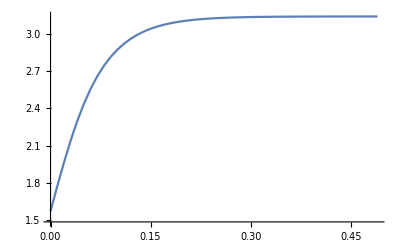

```mathematica
ListLinePlot[RK3[h, Pi/2, 0,1/2, 0.01], PlotRange->All]
```

```mathematica
(*2*)
RK4[du_,du0_, t_,T_, h_]:=Module[
{alphas,betas, p,n,y, i,k1,k2,k3,k4},

n = Floor[(T-t)/h];

y= Table[0, n];
y[[1]]=du0;

For[i=2, i≤n,i++,
k1 = h*du[t+(i-1)*h, y[[i-1]]]//N;
k2 = h*du[t+(i-1)*h+1/2 h, y[[i-1]]+1/2 k1]//N;
k3=h*du[t+(i-1)*h+1/2 h, y[[i-1]]+1/2 k2]//N;
k4 = h*du[t+(i-1)*h+2/3 h,y[[i-1]]+k3]//N;
y[[i]]=y[[i-1]]+(1/6 k1+1/3 k2+1/3 k3+1/6 k4)//N; 
];

ret = Table[{t+(i-1)*h, y[[i]]}, {i,1,n}]
]
```

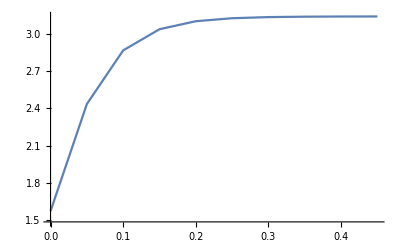

```mathematica
ListLinePlot[RK4[h, Pi/2, 0,1/2, 0.05], PlotRange->All]
```

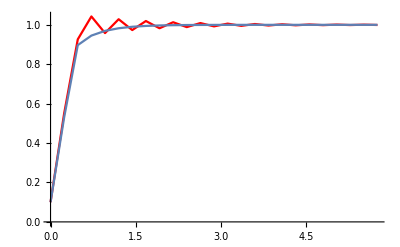
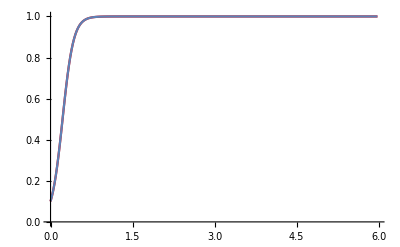

```mathematica
(*3*)
g[t_,u_]:=10u(1-u);
l = {6/25,6/250};
Table[
Show[{
ListLinePlot[RK3[g, 0.1, 0,6, l[[i]]], PlotRange->All, PlotStyle->Red],
ListLinePlot[RK4[g,0.1, 0,6, l[[i]]], PlotRange->All]
}
],
{i,1,2}
]
```

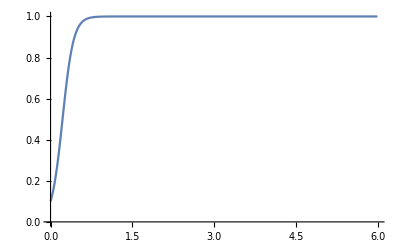

```mathematica
ListLinePlot[RK4[g,0.1, 0,6, 6/400], PlotRange->All]
```

```mathematica
(*4*)
```

```mathematica
alpha[du_,du0_, t_,T_, h_, metod_]:=Module[
{res},
l = {1,2,4};
res = Table[metod[du,du0, t,T, h/l[[i]]],{i,1,3}];
(*Print[res[[1]][[1,2]]];*)

ret = Table[{res[[1]][[i,1]],Log[Abs[(res[[1]][[i,2]]-res[[2]][[1+2(i-1),2]])/(res[[2]][[1+2(i-1),2]]-res[[3]][[1+4(i-1),2]])]]/Log[2]}//N,{i,1,Length[res[[1]]]}]
]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

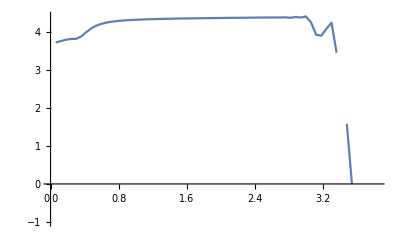

```mathematica
ListLinePlot[alpha[g, 0.1, 0,6, 6/100, RK4], PlotRange->All]
```

```mathematica
b[t_]:=Piecewise[{{1, 0≤t<=2}, {3, t>2}}]
r[t_,u_]:=-b[t]*u+t;
a[t_]:=Piecewise[{{t-1+2 E^-t, 0≤t≤2}, {1/3 t-1/9+E^(-3t)(4/9 E^6+2 E^4), t>2}}]
```

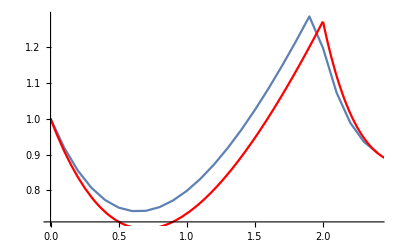

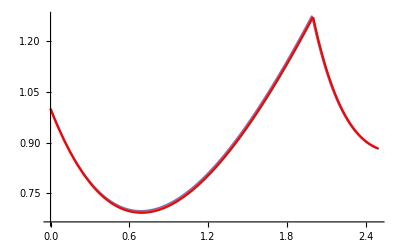

```mathematica
Show[{
ListLinePlot[RK3[r,1,0,2.5,0.1]],
Plot[a[t],{t,0,2.5},PlotStyle->Red]
}]
Show[{
ListLinePlot[RK3[r,1,0,2.5,0.01]],
Plot[a[t],{t,0,2.5},PlotStyle->Red]
}]
```

```mathematica
res = RK3[r,1,0,10,0.1]
```

{{0.,1},{0.1,0.919183},{0.2,0.855574},{0.3,0.807536},{0.4,0.773585},{0.5,0.752382},{0.6,0.742714},{0.7,0.743482},{0.8,0.753694},{0.9,0.772451},{1.,0.798939},{1.1,0.832424},{1.2,0.872238},{1.3,0.91778},{1.4,0.968505},{1.5,1.02392},{1.6,1.08358},{1.7,1.14707},{1.8,1.21404},{1.9,1.28416},{2.,1.19648},{2.1,1.07214},{2.2,0.988721},{2.3,0.935598},{2.4,0.90491},{2.5,0.890836},{2.6,0.889064},{2.7,0.896402},{2.8,0.910486},{2.9,0.929565},{3.,0.952343},{3.1,0.97786},{3.2,1.00541},{3.3,1.03445},{3.4,1.06461},{3.5,1.0956},{3.6,1.12719},{3.7,1.15923},{3.8,1.19161},{3.9,1.22424},{4.,1.25705},{4.1,1.28999},{4.2,1.32304},{4.3,1.35616},{4.4,1.38934},{4.5,1.42255},{4.6,1.4558},{4.7,1.48907},{4.8,1.52236},{4.9,1.55566},{5.,1.58896},{5.1,1.62228},{5.2,1.6556},{5.3,1.68892},{5.4,1.72224},{5.5,1.75557},{5.6,1.7889},{5.7,1.82223},{5.8,1.85556},{5.9,1.88889},{6.,1.92223},{6.1,1.95556},{6.2,1.98889},{6.3,2.02222},{6.4,2.05556},{6.5,2.08889},{6.6,2.12222},{6.7,2.15556},{6.8,2.18889},{6.9,2.22222},{7.,2.25556},{7.1,2.28889},{7.2,2.32222},{7.3,2.35556},{7.4,2.38889},{7.5,2.42222},{7.6,2.45556},{7.7,2.48889},{7.8,2.52222},{7.9,2.55556},{8.,2.58889},{8.1,2.62222},{8.2,2.65556},{8.3,2.68889},{8.4,2.72222},{8.5,2.75556},{8.6,2.78889},{8.7,2.82222},{8.8,2.85556},{8.9,2.88889},{9.,2.92222},{9.1,2.95556},{9.2,2.98889},{9.3,3.02222},{9.4,3.05556},{9.5,3.08889},{9.6,3.12222},{9.7,3.15556},{9.8,3.18889},{9.9,3.22222}}

```mathematica
a[1.9]//N
```

1.19914

```mathematica
tab = Table[{res[[i,1]], a[res[[i,1]]]-res[[i,2]]},{i,1,Length[res]}]
```

{{0.,0.},{0.1,-0.0095085},{0.2,-0.0181129},{0.3,-0.0258991},{0.4,-0.032945},{0.5,-0.0393209},{0.6,-0.0450906},{0.7,-0.0503117},{0.8,-0.0550363},{0.9,-0.0593116},{1.,-0.0631805},{1.1,-0.0666815},{1.2,-0.0698496},{1.3,-0.0727164},{1.4,-0.0753107},{1.5,-0.0776583},{1.6,-0.0797826},{1.7,-0.081705},{1.8,-0.0834446},{1.9,-0.0850188},{2.,0.0741928},{2.1,0.0465173},{2.2,0.0259647},{2.3,0.0107017},{2.4,-0.000632857},{2.5,-0.00905009},{2.6,-0.0153008},{2.7,-0.0199426},{2.8,-0.0233897},{2.9,-0.0259494},{3.,-0.0278502},{3.1,-0.0292618},{3.2,-0.0303099},{3.3,-0.0310883},{3.4,-0.0316663},{3.5,-0.0320955},{3.6,-0.0324142},{3.7,-0.0326508},{3.8,-0.0328265},{3.9,-0.032957},{4.,-0.0330539},{4.1,-0.0331259},{4.2,-0.0331793},{4.3,-0.0332189},{4.4,-0.0332484},{4.5,-0.0332703},{4.6,-0.0332865},{4.7,-0.0332986},{4.8,-0.0333075},{4.9,-0.0333142},{5.,-0.0333191},{5.1,-0.0333228},{5.2,-0.0333255},{5.3,-0.0333275},{5.4,-0.033329},{5.5,-0.0333301},{5.6,-0.0333309},{5.7,-0.0333316},{5.8,-0.033332},{5.9,-0.0333324},{6.,-0.0333326},{6.1,-0.0333328},{6.2,-0.0333329},{6.3,-0.033333},{6.4,-0.0333331},{6.5,-0.0333332},{6.6,-0.0333332},{6.7,-0.0333332},{6.8,-0.0333333},{6.9,-0.0333333},{7.,-0.0333333},{7.1,-0.0333333},{7.2,-0.0333333},{7.3,-0.0333333},{7.4,-0.0333333},{7.5,-0.0333333},{7.6,-0.0333333},{7.7,-0.0333333},{7.8,-0.0333333},{7.9,-0.0333333},{8.,-0.0333333},{8.1,-0.0333333},{8.2,-0.0333333},{8.3,-0.0333333},{8.4,-0.0333333},{8.5,-0.0333333},{8.6,-0.0333333},{8.7,-0.0333333},{8.8,-0.0333333},{8.9,-0.0333333},{9.,-0.0333333},{9.1,-0.0333333},{9.2,-0.0333333},{9.3,-0.0333333},{9.4,-0.0333333},{9.5,-0.0333333},{9.6,-0.0333333},{9.7,-0.0333333},{9.8,-0.0333333},{9.9,-0.0333333}}

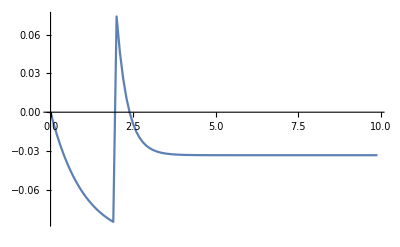

```mathematica
ListLinePlot[tab, PlotRange->All]
```